```mathematica
g = Range[1,8, 1];
e = Range[9, 24,1];
e = Delete[e, {{14-8}, {15-8}, {20-8}}]; (* при q=1 неактивны *)
```

## Константы

```mathematica
τ=1 (* τ *);
τTrue = 27.2  10^-9;(* c *)
λ0 = 670.951 10^-9; (* м *)
cLight = 3 10^8 (* м/c *);
```

## Добавим частоты

```mathematica
ω0 = 2 π cLight/λ0 τTrue;
ω1 = 803.5 10^6 τTrue;
ω2 = 9.2 10^6 τTrue;
ω3 = 6.2 10^6 τTrue;
ω4 = 3.1 10^6 τTrue;
```

## Научимся в C_(β α)

```mathematica
ClearAll[CRabi];
CRabi[{F2_, mF2_},{F1_, mF1_}, q_ : 1, 
Ι_ : 3/2, S_ : 1/2, J1_ : 1/2, J2_ : 3/2, L1_ : 0, L2_ : 1] := 
(-1)^(1/2 q(1+q) + 1 + 2 F1 - mF1 + Ι + J2 +S +L2 + J1)√((2 F1 + 1)(2 F2 + 1)(2 J1 +1)(2 J2 + 1)(2 L1 + 1)) ThreeJSymbol[{F1, -mF1},{1,q},{F2, mF2}] SixJSymbol[{J1,F1, Ι},{F2,J2,1}] SixJSymbol[{L1,J1,S},{J2,L2,1}] /; q + mF2 - mF1 == 0 && Abs[F1-F2] ≤ 1;
CRabi[{F2_, mF2_}, {F1_, mF1_}, q_ : 1, 
Ι_ : 3/2, S_ : 1/2, J1_ : 1/2, J2_ : 1/2, L1_ : 0, L2_ : 1] := 0;
```

```mathematica
ClearAll[objFmF];
objFmF = <|
1->{1, -1},2->{1,0},3->{1, 1} ,
4->{2, -2},5->{2, -1},6->{2, 0},7->{2, 1},8->{2, 2},
9->{3, -3},10->{3, -2},11->{3, -1},12->{3, 0},13->{3, 1},14->{3, 2},15->{3, 3},
16->{2, -2},17->{2, -1},18->{2, 0},19->{2, 1},20->{2, 2},
21->{1, -1},22->{1, 0},23->{1, 1},
24->{0, 0}
|>;
objωR = <|
1->0,2->0,3->0 ,
4->ω1,5->ω1,6->ω1,7->ω1,8->ω1,
9->0,10->0,11->0,12->0,13->0,14->0,15->0,
16->ω2,17->ω2,18->ω2,19->ω2,20->ω2,
21->ω3,22->ω3,23->ω3,
24->ω4
|>;
```

```mathematica
ClearAll[GetωR, GetCRabi,GetΩRabi];
GetωR[β_, α_] := GetωR[β, α] = ω0 + objωR[β] - objωR[α];
GetCRabi[β_, α_] :=GetCRabi[β, α] = CRabi[objFmF[β],objFmF[α]];
GetΩRabi[β_, α_, s_:1] :=0.17/τ √s GetCRabi[β, α];
```

```mathematica
(* чтобы сохранялись диагональные члены, ПОДГОН*)
ClearAll[SCALE];
SCALE[β_]:=SCALE[β]= Total@Map[GetCRabi[β,#]^2&, g];
```

```mathematica
ClearAll[SCALE2];
SCALE2[α_]:= SCALE2[α]=Total@Map[GetCRabi[#,α]^2&, e];
```

## Охапка переменных

```mathematica
ListρRe = Flatten@Outer[ρRe,e,g]; 
ListρIm = Flatten@Outer[ρIm,e,g]; 
Listρα = Map[ρ[#, #]&, g]; 
Listρβ = Map[ρ[#, #]&, e]; 
ListFull = Join[Listρα, Listρβ, ListρIm, ListρRe];
Print["Всего переменных: ",Length@ListFull]

varsI = ListFull;
varsII = Table[Unique[], {i, 1, Length[varsI], 1}];
subsI = Table[varsI[[i]]-> varsII[[i]], {i, 1, Length@varsI, 1}];
subsII = Table[varsII[[i]]-> varsI[[i]], {i, 1, Length@varsI, 1}];
```

Всего переменных: 229

## Уравнение на эволюцию

```mathematica
ClearAll[GetGroundEvol, GetExitedEvol, GetReDiagonalEvol, GetImDiagonalEvol];
GetGroundEvol[ζ_, s_, α_] := 2ζ Total@Map[ρIm[#, α]GetΩRabi[#, α, s]&, e] + 1/τ Total@Map[ ρ[#, #]N@(GetCRabi[#, α]^2)&, e];
GetExitedEvol[ζ_,s_, β_] := -2 ζ Total@Map[ρIm[β, #]GetΩRabi[β, #, s]&, g] - 1/τ ρ[β, β]SCALE[β];
GetReDiagonalEvol[δ_,s_, β_, α_] := (GetωR[β, α]-ω0 - δ)ρIm[β, α] -1/(2τ)ρRe[β, α]SCALE[β];
GetImDiagonalEvol[δ_,s_, ζ_, β_, α_] := ζ GetΩRabi[β, α, s](ρ[β, β] - ρ[α, α])-(GetωR[β, α]-ω0 - δ)ρRe[β, α] -1/(2τ)ρIm[β, α]SCALE[β];
```

```mathematica
ClearAll[EQS]; 
EQS = Join[
FullSimplify@Map[GetGroundEvol[ζ0,s0, #]&, g], 
FullSimplify@Map[GetExitedEvol[ζ0,s0, #]&, e], 
FullSimplify@Flatten@Outer[GetImDiagonalEvol[δ0,s0, ζ0, #1, #2]&,e,g] ,  
FullSimplify@Flatten@Outer[GetReDiagonalEvol[δ0, s0, #1, #2]&,e,g] ];
```

```mathematica
ClearAll[GetCoefs];
GetCoefs[δ_, s_:1, ζ_:1]:=Module[{eqsI, eqsII, coefs, coefsSA},
eqsI = EQS/.{ζ0 -> ζ,δ0-> δ, s0-> s};
eqsII = eqsI /. subsI;
coefs = Normal@CoefficientArrays[eqsII,varsII][[2]] ;
coefsSA = SparseArray[coefs];
coefsSA
]
```

```mathematica
coefsSA =GetCoefs[0, 10000];
 coefsSA// MatrixRank
exp = MatrixExp[500 coefsSA];
```

224

```mathematica
exp[[;;21, ;;21]] // ArrayPlot
```

-Graphics-

```mathematica
ClearAll[GetLevels];
GetLevels[δ_, s_, ζ_:1] := Module[{f, g1, g2, e0, e1,e2,e3, res, Ν, i,data, coefsSA,exp},
Ν = 100;
coefsSA =GetCoefs[δ, s, ζ];
exp = MatrixExp[500 coefsSA];
data = Table[
IC = Join[Normalize[ RandomReal[{0, 1}, 21], Total], ConstantArray[0, Length@varsI-21]];
f = exp.IC;
g1 = Total[f[[ 1;;3]]];
g2 = Total[f[[ 4;;8]]];
e3 = Total[f[[ 9;;13]]];
e2 = Total[f[[ 14;;17]]];
e1 = Total[f[[ 18;;20]]];
e0 = Total[f[[ 21]]];
{g1, g2, e3, e2, e1, e0}
, {i, 1, Ν}];
res = 1/Ν Total[data, {1}] ;
res
];
```

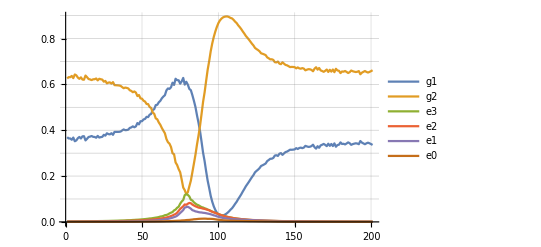

```mathematica
δs = Range[-100, 100,1];
vals = Transpose@ParallelMap[GetLevels[#, 5000]&,δs];
ListLinePlot[vals, PlotRange->Full, PlotLegends->{"g1", "g2", "e3", "e2","e1", "e0"}, GridLines->{Automatic, Range[0, 1, 0.1]}]
```

## Поглощение

```mathematica
inds = {1,2,3,4,5,6,7,8,9,10,11,12,13,16,17,18,19,21,22,23,24};
```

```mathematica
coefsSA =GetCoefs[0, 100000, 1];
exp = MatrixExp[500 coefsSA];

 IC = Join[Normalize[ RandomReal[{0, 1}, 21], Total], ConstantArray[0, Length@varsI-21]];
f = exp.IC;

+Total@Table[SCALE2[inds[[i]]]f[[i]], {i, 1, 8}]-Total@Table[SCALE[inds[[i]]]f[[i]], {i, 9, 21}]
```

0.045007

```mathematica
ClearAll[GetAbs];
GetAbs[f_]:=Total@Table[SCALE2[inds[[χ]]]f[[χ]], {χ, 1, 8}]-Total@Table[SCALE[inds[[χ]]]f[[χ]], {χ, 9, 21, 1}];
```

```mathematica
ClearAll[GetLevels2];
GetLevels2[δ_, s_, ζ_:1] := Module[{f, g1, g2, e0, e1,e2,e3, res, Ν, i,data, coefsSA,exp, abs, IC},
Ν = 1000;
coefsSA =GetCoefs[δ, s, ζ];
exp = MatrixExp[500 coefsSA];
data = Table[
IC = Join[Normalize[ RandomReal[{0, 1}, 21], Total], ConstantArray[0, Length@varsI-21]];
exp.IC
, {i, 1, Ν}];
res = 1/Ν Total[data, {1}] ;
res
];
```

```mathematica
δs = Range[-5, 5,1];
GetAbs@GetLevels2[0, 100]; // AbsoluteTiming
```

{0.0585112,Null}

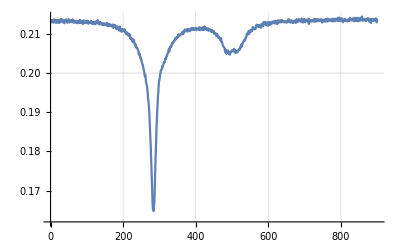

```mathematica
δs = Range[-50, 40,0.1];
abs5 = ParallelMap[GetAbs[GetLevels2[#, 100]]&,δs];
ListLinePlot[abs5, PlotRange->Full, GridLines->{Automatic, Range[0, 1, 0.1]}]
```

```mathematica
ClearAll[GetEst];
GetEst[δ_, s_:100]:= Module[{f},
f = Normal@GetLevels2[δ, s];
Total@Table[GetCRabi[βsInds[[χ]], αsInds[[χ]]]f[[χ]], {χ, 22, 229}]
]
```

```mathematica
ClearAll[GetEst2];
GetEst2[δ_, s_:100]:= Module[{f},
f = Normal@GetLevels2[δ, s];
Total@Table[GetCRabi[βsInds[[χ]], αsInds[[χ]]]f[[χ]], {χ, 22, 125}]
]
```

```mathematica
βsInds = Map[#[[1]]&, varsI];
αsInds = Map[#[[2]]&, varsI];
```

```mathematica
δs = Range[-50, 40,0.1];
est = ParallelMap[GetEst2[#,10]&,δs];
ListLinePlot[est, PlotRange->Full]
```

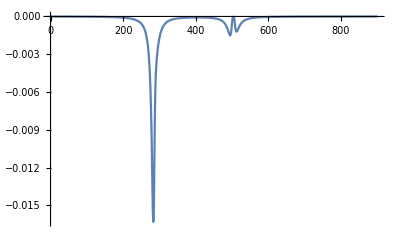

## Доплер